```mathematica
Arms[x1_,x2_,x3_,x4_]:=FindRoot[
{Sum[Cos[Subscript[θ, i]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]],{i,1,4}]==0,
Sum[Cos[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,4}]==0},
{{Subscript[θ, 1],x1},{Subscript[θ, 2],x2},{Subscript[θ, 3],x3},{Subscript[θ, 4],x4}},
MaxIterations->1000]
TraceOut[x_,y_]:=FindRoot[
{Subscript[L, 1] Cos[Subscript[θ, 1]]+Subscript[L, 2] Cos[Subscript[θ, 2]]==x,
Subscript[L, 1] Sin[Subscript[θ, 1]]+Subscript[L, 2] Sin[Subscript[θ, 2]]==y
},
{{Subscript[θ, 1],0.3,0,π},{Subscript[θ, 2],1.5,-π,π}}
]
```

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.07420;Subscript[δ, 3]=-0.04497;Subscript[δ, 4]=-0.00179;
sol=Arms[3,1,2,1] (*Set 1*)
```

{θ_1→1.88484,θ_2→0.628205,θ_3→5.65487,θ_4→-1.88514}

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.02742;Subscript[δ, 3]=0.02853;Subscript[δ, 4]=-0.07487;
sol=Arms[2,1,6,4] (*Set 2*)
```

{θ_1→1.8849,θ_2→0.628398,θ_3→5.65479,θ_4→4.39828}

```mathematica
Subscript[δ, 1]=-0.02412;Subscript[δ, 2]=-0.16026;Subscript[δ, 3]=0.27843;Subscript[δ, 4]=-0.27794;
sol=Arms[2,0.5,6,4] (*Set 3*)
```

{θ_1→1.88503,θ_2→0.628328,θ_3→5.6549,θ_4→4.39828}

```mathematica
Subscript[δ, 1]=0.07272;Subscript[δ, 2]=1.20678;Subscript[δ, 3]=4.78410;Subscript[δ, 4]=1.3022;
sol=Arms[2,0.5,6,4] (*Set 4*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{θ_1→1.06552,θ_2→-0.982549,θ_3→5.51952,θ_4→2.43605}

```mathematica
Subscript[δ, 1]=-0.71895;Subscript[δ, 2]=0.71895;Subscript[δ, 3]=-0.52670;Subscript[δ, 4]=-0.15747;
sol=Arms[2,0.5,6,4] (*Set 5*)
```

{θ_1→1.11641,θ_2→0.261798,θ_3→5.28677,θ_4→3.46502}

{{0,0},{0.438912,0.89853},{1.40484,1.15735},{1.94815,0.317818},{1.,1.11022×10^-16}}

{{0,0},{0.922048,0.387076},{1.88797,0.645894},{1.93563,-0.35297},{1.,1.11022×10^-16}}

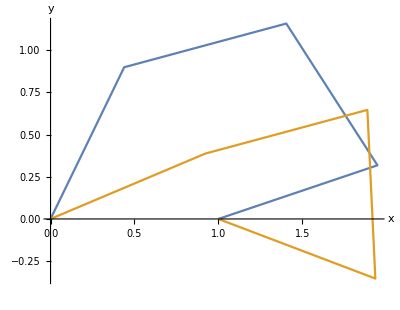

```mathematica
start = Prepend[Table[{Sum[Cos[Subscript[θ, i]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
end = Prepend[Table[{Sum[Cos[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
ListPlot[{start,end}, Joined->True,AspectRatio->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
p11={};
Do[{
ans=TraceOut[d[[a]][[1]],d[[a]][[2]]];
If[(Abs[Sum[Subscript[L, i] Cos[Subscript[θ, i]]/.ans,{i,1,2}]-d[[a]][[1]]]>10^-4 ||Abs[Sum[Subscript[L, i] Sin[Subscript[θ, i]],{i,1,2}]-d[[a]][[2]]]>10^-4)||(((des/.ans)>0)&&((t/.tsol[[1]]/.ans)<1)),AppendTo[p11,{d[[a]][[1]],d[[a]][[2]]}],Print[des/.ans]]
},{a,1,Length[d]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::reged: The point {0.,1.70305} is at the edge of the search region {0.,3.14159} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,1.67667} is at the edge of the search region {0.,3.14159} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,1.65014} is at the edge of the search region {0.,3.14159} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

```mathematica
Export["Bottom4.dat",p11]
```

Bottom4.dat

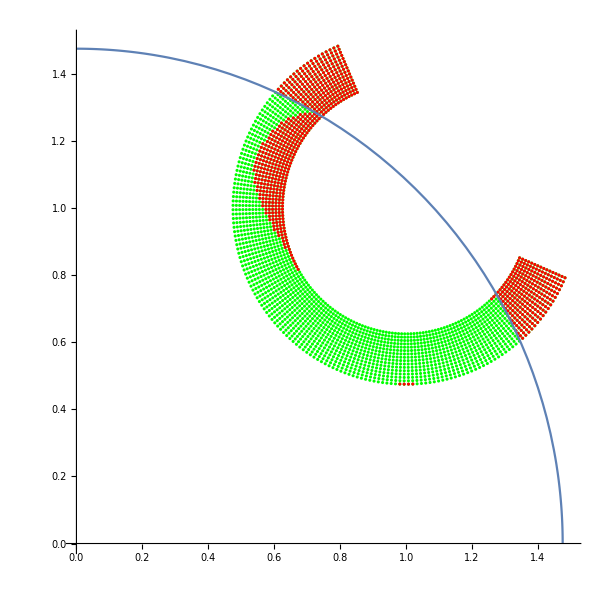

```mathematica
Show[ListPlot[{d,p11},PlotRange->{{0,1.5},{0,1.5}},AspectRatio->Automatic,PlotStyle->{Green,Red}],
ParametricPlot[{(Subscript[L, 1]+Subscript[L, 2])Cos[t],(Subscript[L, 1]+Subscript[L, 2])Sin[t]},{t,0,π/2}]]
```

```mathematica
Subscript[L, 1]=1
Subscript[L, 2]=475/1000
```

1

19/40

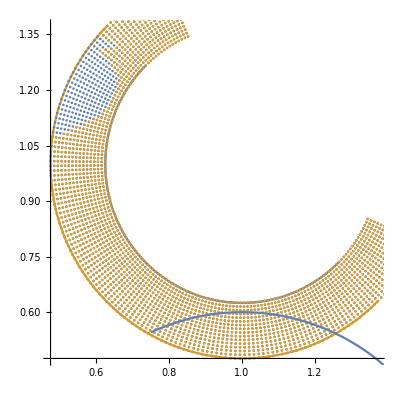

```mathematica
d=ArrayReshape[Table[{1+r Cos[t],1+r Sin[t]},{r,0.375,0.525,0.01},{t,3 π/4-0.38,7 π/4+0.38,0.025}],{16 157,2}];
Show[ParametricPlot[{{1+0.375Cos[2π t],1+0.375Sin[2π t]},{1+0.525Cos[2π t],1+0.525Sin[2π t]}},{t,3/8,7/8}],ListPlot[{d,p11},AspectRatio->Automatic],
ParametricPlot[{1+0.6Cos[t],0.6Sin[t]},{t,0,2}]]
```

```mathematica
Export["Total.dat",d]
```

Total.dat

```mathematica
N[ArcTan[1/55 (64+3 √119)]]
```

1.05377

```mathematica
Export["Lower.dat",q]
```

Lower.dat

```mathematica
tsol=Simplify[Solve[Collect[Expand[(Subscript[L, a] Cos[Subscript[θ, 1]]+Subscript[L, b] Cos[Subscript[θ, 2]]t-1)^2+(Subscript[L, a] Sin[Subscript[θ, 1]]+Subscript[L, b] Sin[Subscript[θ, 2]]t-1)^2-(R)^2==0],t],t]]
```

{{t→((Cos[θ_2]+Sin[θ_2]-Cos[θ_1-θ_2] L_a) L_b-√((-1+R^2+Sin[2 θ_2]+2 Sin[θ_1-θ_2] (Cos[θ_2]-Sin[θ_2]) L_a-Sin[θ_1-θ_2]^2 L_a^2) L_b^2))/L_b^2},{t→((Cos[θ_2]+Sin[θ_2]-Cos[θ_1-θ_2] L_a) L_b+√((-1+R^2+Sin[2 θ_2]+2 Sin[θ_1-θ_2] (Cos[θ_2]-Sin[θ_2]) L_a-Sin[θ_1-θ_2]^2 L_a^2) L_b^2))/L_b^2}}

```mathematica
des=-87+64 Cos[Subscript[θ, 1]]-64 Cos[Subscript[θ, 1]-2 Subscript[θ, 2]]+32 Cos[2 (Subscript[θ, 1]-Subscript[θ, 2])]+64 Sin[Subscript[θ, 1]]+64 Sin[Subscript[θ, 1]-2 Subscript[θ, 2]]+64 Sin[2 Subscript[θ, 2]]
```

-87+64 Cos[θ_1]-64 Cos[θ_1-2 θ_2]+32 Cos[2 (θ_1-θ_2)]+64 Sin[θ_1]+64 Sin[θ_1-2 θ_2]+64 Sin[2 θ_2]